```mathematica
SetDirectory[NotebookDirectory[]];
```

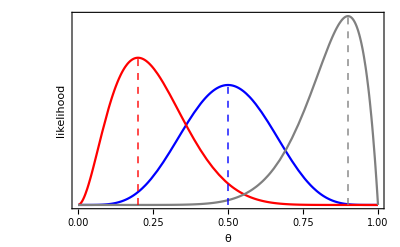

```mathematica
gFinal=Plot[{Likelihood[BinomialDistribution[10,θ],{5}],Likelihood[BinomialDistribution[10,θ],{2}],Likelihood[BinomialDistribution[10,θ],{9}]},{θ,0,1},PlotStyle->{Blue,Red,Gray},Epilog->{{Dashed,Blue,Line[{{0.5,0},{0.5,Likelihood[BinomialDistribution[10,0.5],{5}]}}]},{Dashed,Red,Line[{{0.2,0},{0.2,Likelihood[BinomialDistribution[10,0.2],{2}]}}]},{Dashed,Gray,Line[{{0.9,0},{0.9,Likelihood[BinomialDistribution[10,0.9],{9}]}}]}},Frame->{True,True,False,False},FrameTicks->{True,False},FrameLabel->{"θ","likelihood"},BaseStyle->{FontSize->Medium}]
```

```mathematica
Export["Distributions_binomialClinicalTrial.pdf",gFinal]
```

Distributions_binomialClinicalTrial.pdf